```mathematica
Clear["Global`*"];tempdir=CreateDirectory[];
Needs["CCompilerDriver`"];
```

# 数值计算导论

申奥 2017012518 计科70

本实验的目的在于观察截断误差、舍入误差与总误差之间的关系，以及机器浮点数对于计算产生的影响。

## 第一题

绘图的基本思路书上已经给出，我们只需要绘出合适的图像即可。

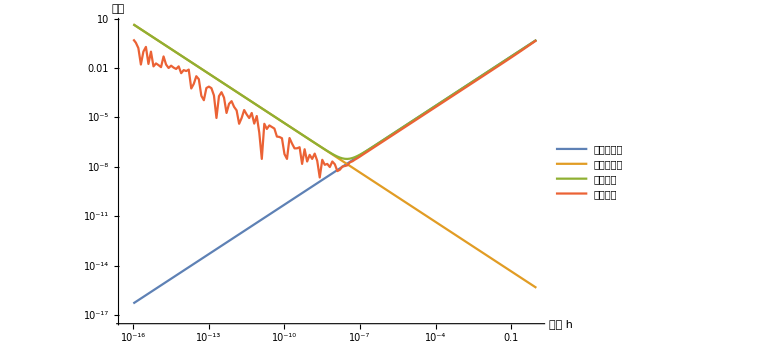

```mathematica
Block[{M=1,ϵ=$MachineEpsilon, (*与课本相同的常数*)
截断误差限,舍入误差限,总误差限,实际误差 (*变量声明*)},
截断误差限[h_]:=(M h)/2;
舍入误差限[h_]:=(2ϵ)/h;
总误差限[h_]:=截断误差限@h+舍入误差限@h;
实际误差[h_]:=((Sin[1+h]-Sin[1])/h)-Cos[1]//Abs;
ListLogLogPlot[Table[{10^h,#[10^h]},{h,-16,0,0.1}](*手动取点160个，防止取点过多图像抖动*)
~Legended~# (*生成图例*)
&/@{截断误差限,舍入误差限,总误差限,实际误差},(*四个函数同时取点*)
Joined->True,AxesLabel->{"步长 h","误差"},ImageSize->Large]
]
```

## 第三题

#### 实验原理

我们首先来分析在单精度浮点数的情况下，结果不变所需要的理论值 i。
我们知道，当所加之数的值小于被加数的机器精度时，求和结果就不会发生变化。

为了求解这一数值，首先我们需要得到  ∑_(i=1)^(n-1) 1/i  在单精度浮点表示下的指数位数值，也就是其以 2 为底的对数值取整。在这一指数下，如果加数的尾数小于机器精度，那么求和结果就不会改变。解方程可以使用FindRoot来完成。

#### 实验过程及代码

对于单精度数，所需的值可以求得为：

```mathematica
singleEpsilon=2^-23;
singleSteps=
n/.FindRoot[(1/n)/2^Floor@Log[2,(∑_(i=1)^(n-1) 1/i)]-singleEpsilon/2,{n,1000000}]
```

2.09715×10^6

对于双精度浮点数，则有：

```mathematica
doubleSteps=n/.FindRoot[(1/n)/2^Floor@Log[2,(∑_(i=1)^(n-1) 1/i)]-($MachineEpsilon)/2,{n,1000000},PrecisionGoal->10]
```

2.81475×10^14

注意后者取值比前者高了 8 个数量级。

我们编写以下C语言代码来验证我们的结果：

```mathematica
singleVerifier=CreateExecutable["
#include<stdio.h>
int main()
{
        float a = 0.0, i=1.0;
        while (a + 1/i != a) {
                a+= 1/i;
                i++;
        }
        printf(\"\\na = %f\\ni = %f\\n\", a, i);
        return 0;
}
","singleVerifier","WorkingDirectory"->tempdir,"TargetDirectory"->$HomeDirectory]
```

/Users/sao/singleVerifier

编译执行，得到：

```mathematica
Import["!"<>QuoteFile[singleVerifier],"Text"]//AbsoluteTiming
```

{0.036042,
a = 15.403683
i = 2097152.000000}

```mathematica
executionTime=Quantity[First@%,"Seconds"]
```

0.036042 s

实际值 2097152 与我们的求解相同。采用双精度浮点数，相加所得的结果准确值应为

```mathematica
Subscript[S, 0]=HarmonicNumber[2097152]//N
```

15.1333

相对误差达：

```mathematica
Abs[15.403683-Subscript[S, 0]]/Subscript[S, 0]
```

0.0178663

超过了 1%。可见单精度浮点数的误差较大。

对于双精度数，之前我们已经求出了所需的 n 值。C语言中单精度程序执行所需时间已经测得，为，一般地假定执行时间与 n 的关系为线性增长，那么对于双精度数，程序终止的时间为：

```mathematica
doubleSteps/singleSteps×executionTime
```

4.83748×10^6 s

也就是：

```mathematica
UnitConvert[%,MixedRadix["Months","Days","Hours","Minutes","Seconds"]]
```

1 25

所以需要大量的时间才能够计算完毕！

## 实验总结

通过本次实验计算的结果，我们知道误差分为舍入误差和截断误差两种，实际计算过程中两种误差叠加共同影响实验误差。同时，浮点数精度通过舍入误差，也会影响计算的复杂度。